FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

平衡点 (x*, y*) = (-0.1697, -7.75)

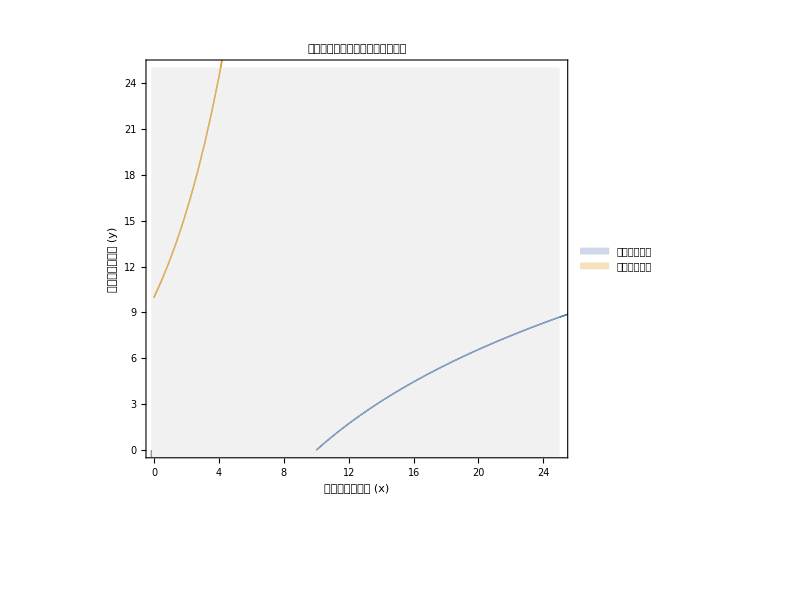

平衡点验证:

甲方条件: x* ≥ x0*p1^(-y*) => -0.1697 ≥ 4.419

乙方条件: y* ≥ y0*p2^(-x*) => -7.75 ≥ 9.628

安全区域存在性条件: p1^y0 * p2^x0 = 0.03744

=> 安全区域D非空

```mathematica
(*甲乙双方核武器竞赛模型分析*)(*参数设置*)x0=10;(*甲方最低威慑阈值*)y0=10;(*乙方最低威慑阈值*)p1=0.9;(*甲方核武器生存概率*)p2=0.8;(*乙方核武器生存概率*)(*定义安全曲线*)f[y_]:=x0*p1^(-y);(*甲方安全曲线:x=x0*p1^(-y)*)g[x_]:=y0*p2^(-x);(*乙方安全曲线:y=y0*p2^(-x)*)(*求解平衡点方程组*)equations={x==f[y],y==g[x]};
initialGuess={{x,15},{y,12}};(*初始猜测值*)solution=FindRoot[equations,initialGuess];
xStar=x/.solution;
yStar=y/.solution;
Print["平衡点 (x*, y*) = (",NumberForm[xStar,4],", ",NumberForm[yStar,4],")"];

(*正确可视化方法：使用ParametricPlot绘制两条曲线*)
plot=ParametricPlot[{{f[y],y},(*甲方安全曲线*){x,g[x]}  (*乙方安全曲线*)},{x,0,25},{y,0,25},PlotRange->{{0,25},{0,25}},AxesLabel->{"甲方核武器数量 (x)","乙方核武器数量 (y)"},PlotLabel->"核武器竞赛安全曲线与平衡点分析",PlotLegends->Placed[{"甲方安全曲线","乙方安全曲线"},Right],Epilog->{{Red,PointSize[0.03],Point[{xStar,yStar}]},Text[Style["平衡点",Red,12],{xStar,yStar},{1.5,-1.5}],{Gray,Dashed,Line[{{xStar,0},{xStar,yStar}}],Line[{{0,yStar},{xStar,yStar}}]},{LightGray,Opacity[0.2],Polygon[{{xStar,yStar},{25,yStar},{25,25},{xStar,25}}],Polygon[{{xStar,yStar},{xStar,25},{25,25},{25,yStar}}]}},ImageSize->600]

(*验证平衡点*)
Print["\n平衡点验证:"];
Print["甲方条件: x* ≥ x0*p1^(-y*) => ",NumberForm[xStar,4]," ≥ ",NumberForm[x0*p1^(-yStar),4]];
Print["乙方条件: y* ≥ y0*p2^(-x*) => ",NumberForm[yStar,4]," ≥ ",NumberForm[y0*p2^(-xStar),4]];

(*存在性条件验证*)
criticalValue=p1^y0*p2^x0;
Print["\n安全区域存在性条件: p1^y0 * p2^x0 = ",NumberForm[criticalValue,4]];
If[criticalValue≥1,Print["=> 安全区域D为空集"],Print["=> 安全区域D非空"]]
```